```mathematica
ExportFunction[file_,fn_]:=Export[file,ArrayFlatten[{{
fn["Grid"],
{fn["ValuesOnGrid"]}ᵀ,
{D[fn[x,y],x][[0]]["ValuesOnGrid"]}ᵀ,
{D[fn[x,y],y][[0]]["ValuesOnGrid"]}ᵀ,
{D[fn[x,y],{x,2}][[0]]["ValuesOnGrid"]}ᵀ,
{D[D[fn[x,y],x],y][[0]]["ValuesOnGrid"]}ᵀ,
{D[fn[x,y],{y,2}][[0]]["ValuesOnGrid"]}ᵀ
}}]]
```

```mathematica
w=.02;
h=1;
r=.2
reg=RegionUnion[Rectangle[{-r/2,-h/2},{-r/2+w,h/2}],Rectangle[{r/2-w,-h/2},{r/2,h/2}],Disk[{-r/2,h/2},r],Disk[{r/2,-h/2},r]]
```

0.2

BooleanRegion[#1||#2||#3||#4&,{Rectangle[{-0.1,-1/2},{-0.08,1/2}],Rectangle[{0.08,-1/2},{0.1,1/2}],Disk[{-0.1,1/2},0.2],Disk[{0.1,-1/2},0.2]}]

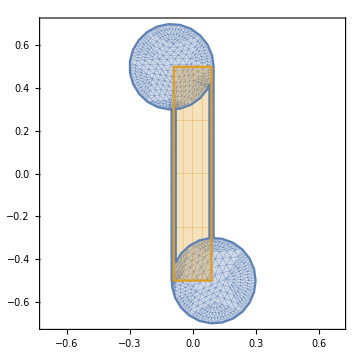

```mathematica
RegionPlot[{Region[reg],Rectangle[{-r/2+w/2,-h/2},{r/2-w/2,h/2}]},PlotRange->{{-.7,.7},{-.7,.7}}]
```

```mathematica
lims={-h/2-r,h/2+r};
soln=NDSolveValue[{∇_{x,y}^2 u[x,y]==0, 
  DirichletCondition[u[x, y]==400w, {x,y}∈Rectangle[{-r/2+w/2,-h/2},{r/2-w/2,h/2}]],  DirichletCondition[u[x, y]==0,Not[{x,y}∈Rectangle[{-r/2+w/2,-h/2},{r/2-w/2,h/2}]]]}, u, {x, y} ∈ 
  reg, Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.0001}}}];
Plot3D[soln[x, y], {x, y} ∈reg,PlotRange->{lims,lims,{0,2w}},PlotPoints->100]
```

-Graphics3D-

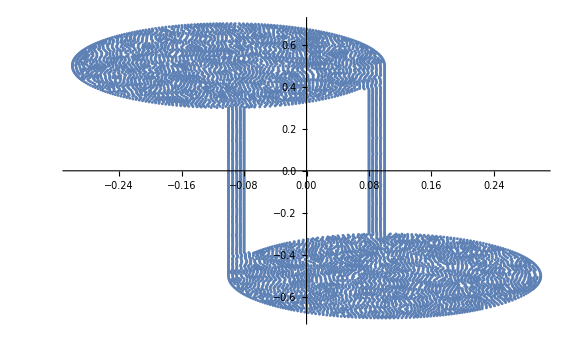

```mathematica
ListPlot[soln["Grid"]]
```

```mathematica
{-D[soln[x,y],y],D[soln[x,y],x]}/.{x->.09,y->0}
```

{1.95541×10^-13,-400.}

```mathematica
ExportFunction["~/continuous-ergodic/v2/rooms/eig151.csv",soln]
```

~/continuous-ergodic/v2/rooms/eig151.csv

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u,{x,y}∈reg,150, Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.0001}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
For[i=1,i<=Length[funs],i++,Print[ExportFunction["~/continuous-ergodic/v2/rooms/eig"<>ToString[i]<>".csv",funs[[i]]]]]
```

~/continuous-ergodic/v2/rooms/eig1.csv

~/continuous-ergodic/v2/rooms/eig2.csv

~/continuous-ergodic/v2/rooms/eig3.csv

~/continuous-ergodic/v2/rooms/eig4.csv

~/continuous-ergodic/v2/rooms/eig5.csv

~/continuous-ergodic/v2/rooms/eig6.csv

~/continuous-ergodic/v2/rooms/eig7.csv

~/continuous-ergodic/v2/rooms/eig8.csv

~/continuous-ergodic/v2/rooms/eig9.csv

~/continuous-ergodic/v2/rooms/eig10.csv

~/continuous-ergodic/v2/rooms/eig11.csv

~/continuous-ergodic/v2/rooms/eig12.csv

~/continuous-ergodic/v2/rooms/eig13.csv

~/continuous-ergodic/v2/rooms/eig14.csv

~/continuous-ergodic/v2/rooms/eig15.csv

~/continuous-ergodic/v2/rooms/eig16.csv

~/continuous-ergodic/v2/rooms/eig17.csv

~/continuous-ergodic/v2/rooms/eig18.csv

~/continuous-ergodic/v2/rooms/eig19.csv

~/continuous-ergodic/v2/rooms/eig20.csv

~/continuous-ergodic/v2/rooms/eig21.csv

~/continuous-ergodic/v2/rooms/eig22.csv

~/continuous-ergodic/v2/rooms/eig23.csv

~/continuous-ergodic/v2/rooms/eig24.csv

~/continuous-ergodic/v2/rooms/eig25.csv

~/continuous-ergodic/v2/rooms/eig26.csv

~/continuous-ergodic/v2/rooms/eig27.csv

~/continuous-ergodic/v2/rooms/eig28.csv

~/continuous-ergodic/v2/rooms/eig29.csv

~/continuous-ergodic/v2/rooms/eig30.csv

~/continuous-ergodic/v2/rooms/eig31.csv

~/continuous-ergodic/v2/rooms/eig32.csv

~/continuous-ergodic/v2/rooms/eig33.csv

~/continuous-ergodic/v2/rooms/eig34.csv

~/continuous-ergodic/v2/rooms/eig35.csv

~/continuous-ergodic/v2/rooms/eig36.csv

~/continuous-ergodic/v2/rooms/eig37.csv

~/continuous-ergodic/v2/rooms/eig38.csv

~/continuous-ergodic/v2/rooms/eig39.csv

~/continuous-ergodic/v2/rooms/eig40.csv

~/continuous-ergodic/v2/rooms/eig41.csv

~/continuous-ergodic/v2/rooms/eig42.csv

~/continuous-ergodic/v2/rooms/eig43.csv

~/continuous-ergodic/v2/rooms/eig44.csv

~/continuous-ergodic/v2/rooms/eig45.csv

~/continuous-ergodic/v2/rooms/eig46.csv

~/continuous-ergodic/v2/rooms/eig47.csv

~/continuous-ergodic/v2/rooms/eig48.csv

~/continuous-ergodic/v2/rooms/eig49.csv

~/continuous-ergodic/v2/rooms/eig50.csv

~/continuous-ergodic/v2/rooms/eig51.csv

~/continuous-ergodic/v2/rooms/eig52.csv

~/continuous-ergodic/v2/rooms/eig53.csv

~/continuous-ergodic/v2/rooms/eig54.csv

~/continuous-ergodic/v2/rooms/eig55.csv

~/continuous-ergodic/v2/rooms/eig56.csv

~/continuous-ergodic/v2/rooms/eig57.csv

~/continuous-ergodic/v2/rooms/eig58.csv

~/continuous-ergodic/v2/rooms/eig59.csv

~/continuous-ergodic/v2/rooms/eig60.csv

~/continuous-ergodic/v2/rooms/eig61.csv

~/continuous-ergodic/v2/rooms/eig62.csv

~/continuous-ergodic/v2/rooms/eig63.csv

~/continuous-ergodic/v2/rooms/eig64.csv

~/continuous-ergodic/v2/rooms/eig65.csv

~/continuous-ergodic/v2/rooms/eig66.csv

~/continuous-ergodic/v2/rooms/eig67.csv

~/continuous-ergodic/v2/rooms/eig68.csv

~/continuous-ergodic/v2/rooms/eig69.csv

~/continuous-ergodic/v2/rooms/eig70.csv

~/continuous-ergodic/v2/rooms/eig71.csv

~/continuous-ergodic/v2/rooms/eig72.csv

~/continuous-ergodic/v2/rooms/eig73.csv

~/continuous-ergodic/v2/rooms/eig74.csv

~/continuous-ergodic/v2/rooms/eig75.csv

~/continuous-ergodic/v2/rooms/eig76.csv

~/continuous-ergodic/v2/rooms/eig77.csv

~/continuous-ergodic/v2/rooms/eig78.csv

~/continuous-ergodic/v2/rooms/eig79.csv

~/continuous-ergodic/v2/rooms/eig80.csv

~/continuous-ergodic/v2/rooms/eig81.csv

~/continuous-ergodic/v2/rooms/eig82.csv

~/continuous-ergodic/v2/rooms/eig83.csv

~/continuous-ergodic/v2/rooms/eig84.csv

~/continuous-ergodic/v2/rooms/eig85.csv

~/continuous-ergodic/v2/rooms/eig86.csv

~/continuous-ergodic/v2/rooms/eig87.csv

~/continuous-ergodic/v2/rooms/eig88.csv

~/continuous-ergodic/v2/rooms/eig89.csv

~/continuous-ergodic/v2/rooms/eig90.csv

~/continuous-ergodic/v2/rooms/eig91.csv

~/continuous-ergodic/v2/rooms/eig92.csv

~/continuous-ergodic/v2/rooms/eig93.csv

~/continuous-ergodic/v2/rooms/eig94.csv

~/continuous-ergodic/v2/rooms/eig95.csv

~/continuous-ergodic/v2/rooms/eig96.csv

~/continuous-ergodic/v2/rooms/eig97.csv

~/continuous-ergodic/v2/rooms/eig98.csv

~/continuous-ergodic/v2/rooms/eig99.csv

~/continuous-ergodic/v2/rooms/eig100.csv

~/continuous-ergodic/v2/rooms/eig101.csv

~/continuous-ergodic/v2/rooms/eig102.csv

~/continuous-ergodic/v2/rooms/eig103.csv

~/continuous-ergodic/v2/rooms/eig104.csv

~/continuous-ergodic/v2/rooms/eig105.csv

~/continuous-ergodic/v2/rooms/eig106.csv

~/continuous-ergodic/v2/rooms/eig107.csv

~/continuous-ergodic/v2/rooms/eig108.csv

~/continuous-ergodic/v2/rooms/eig109.csv

~/continuous-ergodic/v2/rooms/eig110.csv

~/continuous-ergodic/v2/rooms/eig111.csv

~/continuous-ergodic/v2/rooms/eig112.csv

~/continuous-ergodic/v2/rooms/eig113.csv

~/continuous-ergodic/v2/rooms/eig114.csv

~/continuous-ergodic/v2/rooms/eig115.csv

~/continuous-ergodic/v2/rooms/eig116.csv

~/continuous-ergodic/v2/rooms/eig117.csv

~/continuous-ergodic/v2/rooms/eig118.csv

~/continuous-ergodic/v2/rooms/eig119.csv

~/continuous-ergodic/v2/rooms/eig120.csv

~/continuous-ergodic/v2/rooms/eig121.csv

~/continuous-ergodic/v2/rooms/eig122.csv

~/continuous-ergodic/v2/rooms/eig123.csv

~/continuous-ergodic/v2/rooms/eig124.csv

~/continuous-ergodic/v2/rooms/eig125.csv

~/continuous-ergodic/v2/rooms/eig126.csv

~/continuous-ergodic/v2/rooms/eig127.csv

~/continuous-ergodic/v2/rooms/eig128.csv

~/continuous-ergodic/v2/rooms/eig129.csv

~/continuous-ergodic/v2/rooms/eig130.csv

~/continuous-ergodic/v2/rooms/eig131.csv

~/continuous-ergodic/v2/rooms/eig132.csv

~/continuous-ergodic/v2/rooms/eig133.csv

~/continuous-ergodic/v2/rooms/eig134.csv

~/continuous-ergodic/v2/rooms/eig135.csv

~/continuous-ergodic/v2/rooms/eig136.csv

~/continuous-ergodic/v2/rooms/eig137.csv

~/continuous-ergodic/v2/rooms/eig138.csv

~/continuous-ergodic/v2/rooms/eig139.csv

~/continuous-ergodic/v2/rooms/eig140.csv

~/continuous-ergodic/v2/rooms/eig141.csv

~/continuous-ergodic/v2/rooms/eig142.csv

~/continuous-ergodic/v2/rooms/eig143.csv

~/continuous-ergodic/v2/rooms/eig144.csv

~/continuous-ergodic/v2/rooms/eig145.csv

~/continuous-ergodic/v2/rooms/eig146.csv

~/continuous-ergodic/v2/rooms/eig147.csv

~/continuous-ergodic/v2/rooms/eig148.csv

~/continuous-ergodic/v2/rooms/eig149.csv

~/continuous-ergodic/v2/rooms/eig150.csv